```mathematica
dir=NotebookDirectory[];
files=FileNames["Angles0deg_*.csv",dir];
```

```mathematica
dir
```

C:\Users\mogue\OneDrive\Escritorio\Pringle data\Excel_Angles_0deg\

```mathematica
process[file_]:=Module[{data,headers,tcol,acol,time,angle},data=Import[file,"CSV"];
headers=First[data];
tcol=First@FirstPosition[headers,"Time"];
acol=First@FirstPosition[headers,"Angle"];
time=data[[All,tcol]];
angle=-data[[All,acol]];
Transpose@{Rest[time],(Rest[angle]-angle[[2]])*Pi/180}];
```

```mathematica
results = AssociationMap[process, files];
```

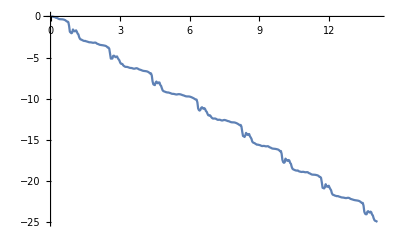
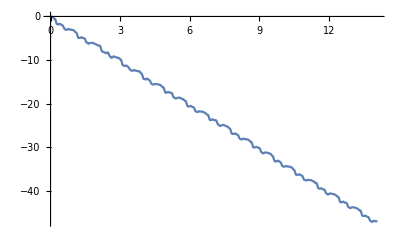
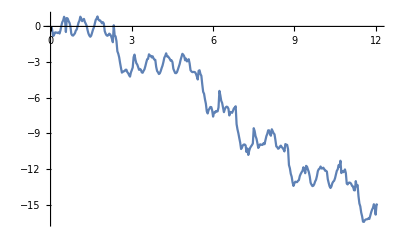
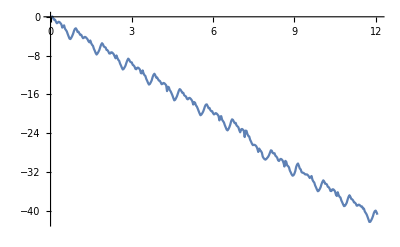
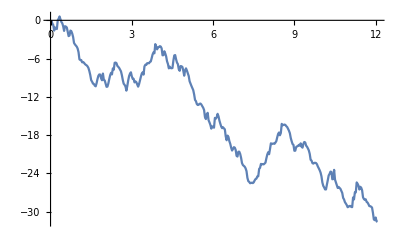
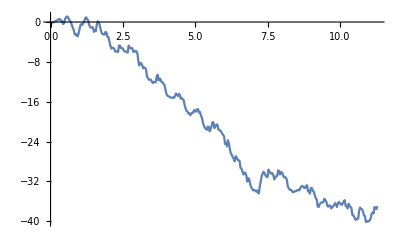

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_4cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}]
```

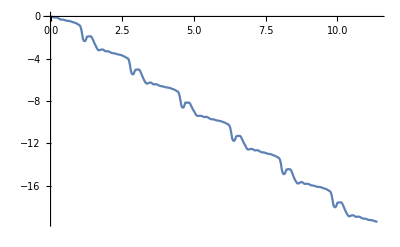
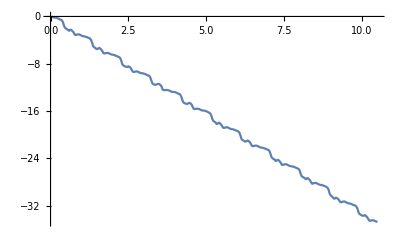
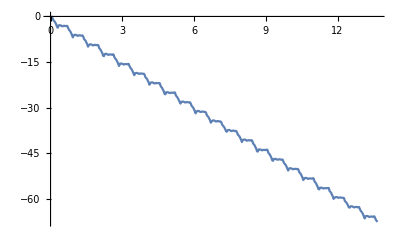
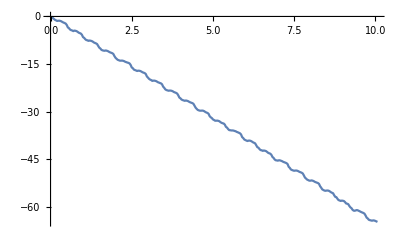
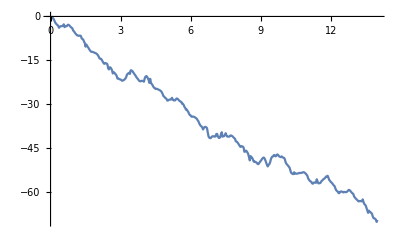
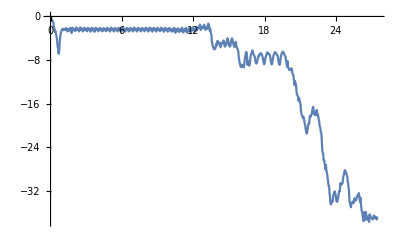

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_5cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}](*i = 6 shows flapping in the movie from t = 1 to 3*)
```

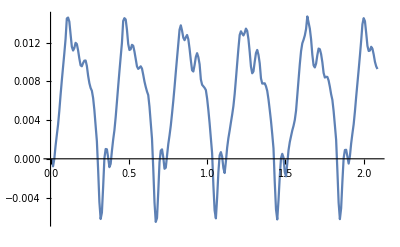
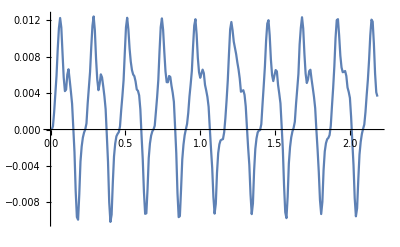
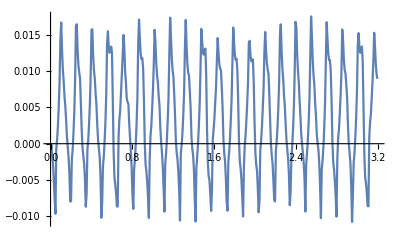
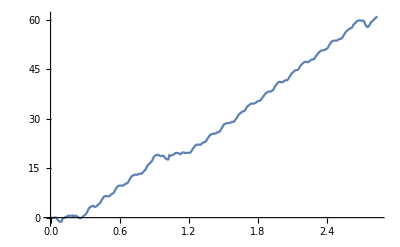
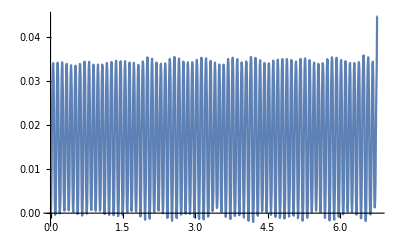
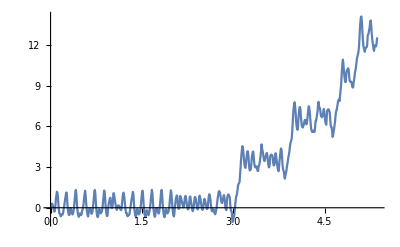

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_6cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}](*i = 6 has flapping and spinning*)
```

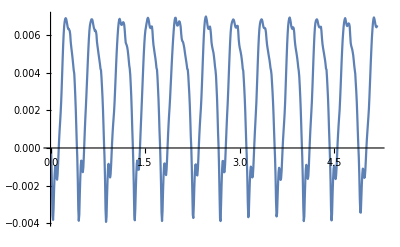
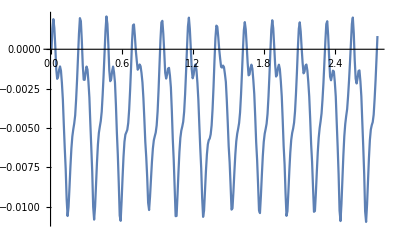
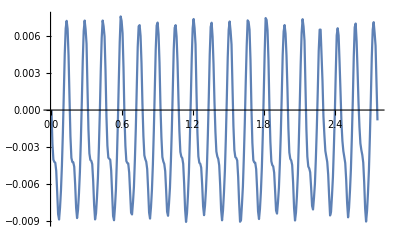
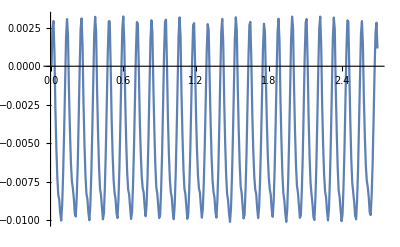
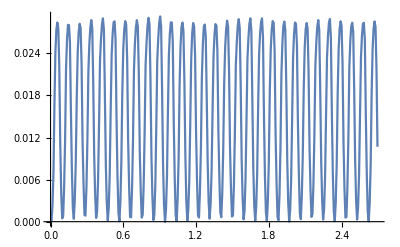
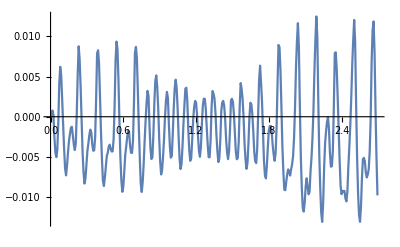

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_7cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}](*i = 6 seems to go from oscillations to flapping to oscillations*)
```

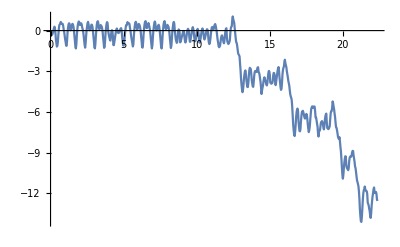
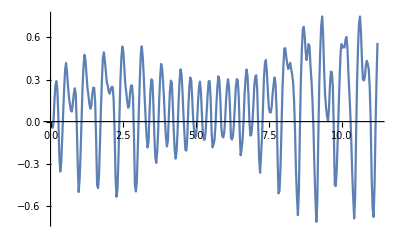
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

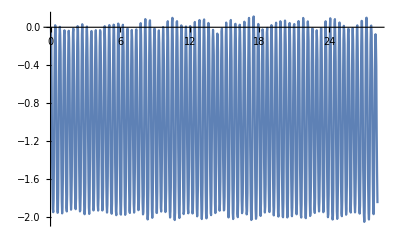
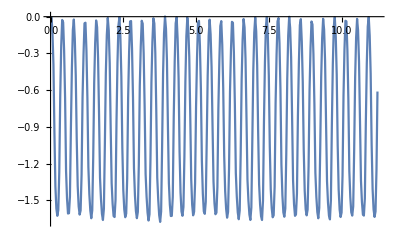
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

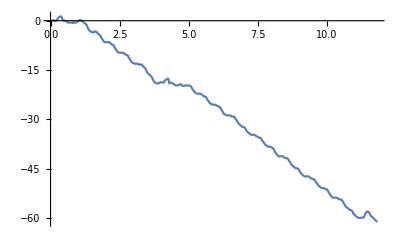
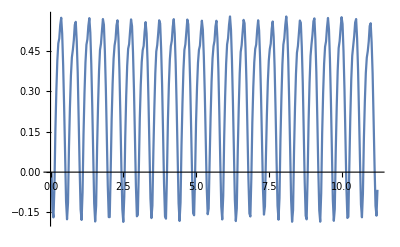
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

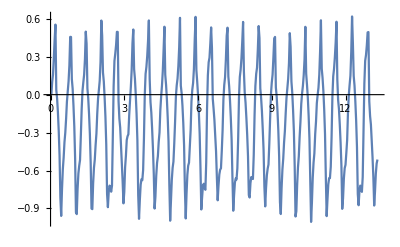
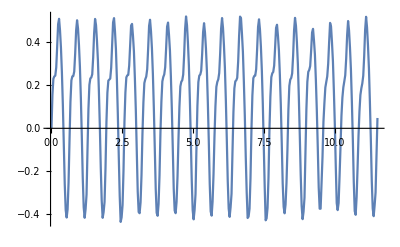
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

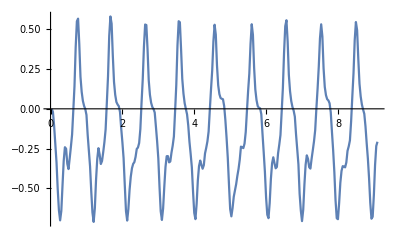
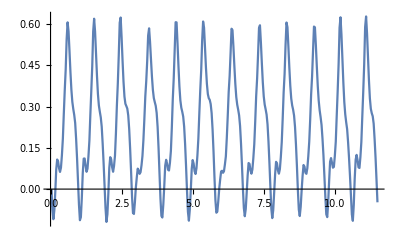
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

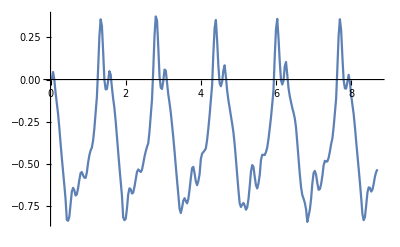
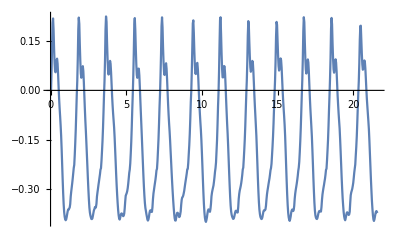
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_"<>ToString[i] <> "cm_6hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_"<>ToString[i] <> "cm_5hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_"<>ToString[i] <> "cm_4hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_"<>ToString[i] <> "cm_3hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_"<>ToString[i] <> "cm_2hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_"<>ToString[i] <> "cm_1hz.csv"]], {i, 4,7}]
```

## Spinning modes/harmonic resonances

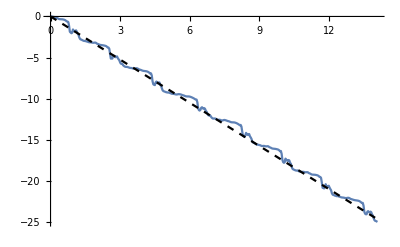
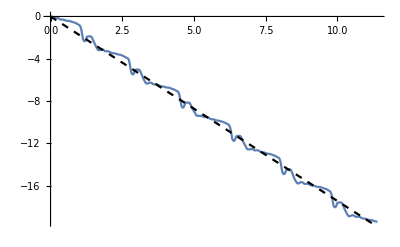

```mathematica
{Show[
ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_4cm_1hz.csv"]],
Plot[{-2Pi x (1/2)5/9}, {x, 0, 14}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]
],Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_5cm_1hz.csv"]],
Plot[{-2Pi x (1/2)5/9}, {x, 0, 14}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]}
```

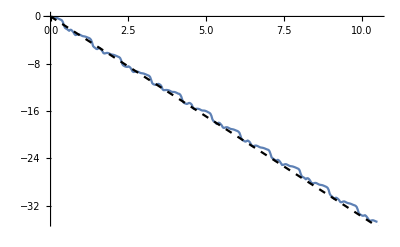
{-Graphics-,-Graphics-}

```mathematica
{Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_5cm_2hz.csv"]],
Plot[{-2Pi x (2/2)7/13}, {x, 0, 14}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]],Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_5cm_2hz.csv"]],
Plot[{-2Pi x (2/2)7/13}, {x, 0, 14}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]}
```

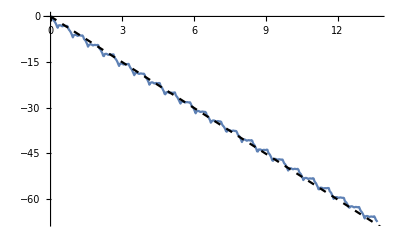

```mathematica
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_5cm_3hz.csv"]],
Plot[{-2Pi x (3/2)8/15}, {x, 0, 14}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
```

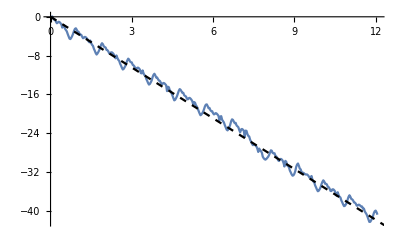
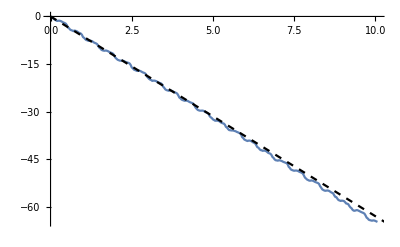
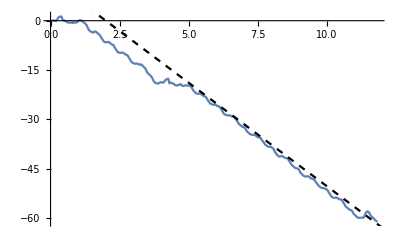

```mathematica
{Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_4cm_4hz.csv"]],
Plot[{-2Pi x (4/2)5/18}, {x, 0, 14}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]], Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_5cm_4hz.csv"]],
Plot[{-2Pi x (4/2)5/10}, {x, 0, 14}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]],Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_6cm_4hz.csv"]],
Plot[{-2Pi (x-2) (4/2)1/2}, {x, 0, 14}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]}
```

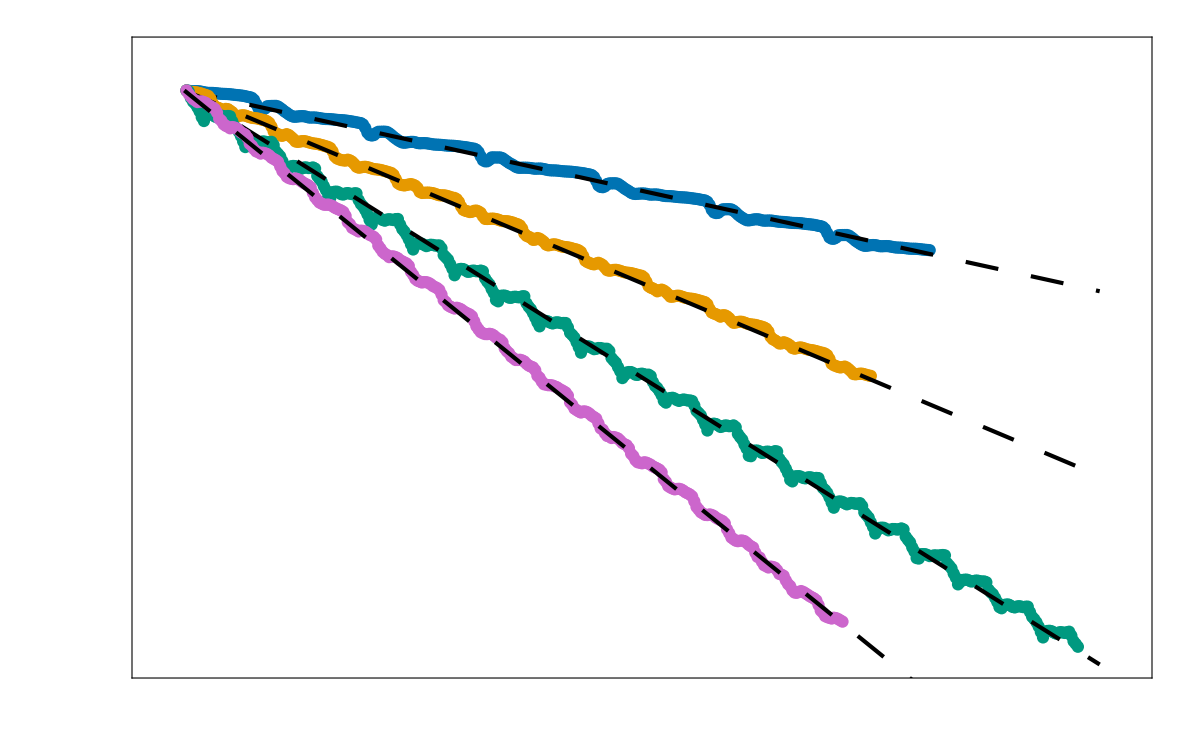

```mathematica
fig = Show[ListPlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_5cm_1hz.csv"], PlotRange->{{-0.5, 14.5}, {-70, 5}}, PlotStyle->{AbsoluteThickness[5], RGBColor[0.0,0.45,0.7]},
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0,14,2}],Table[{y,, {0.01, 0}},{y,-70,5,10}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1200
],
Plot[{-2Pi x (1/2)5/9}, {x, 0, 14}, PlotStyle->{{AbsoluteThickness[3],Dashing[{0.02,0.02}],Black}}], ListPlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_5cm_2hz.csv"], PlotStyle->{AbsoluteThickness[5], RGBColor[0.9,0.6,0.0]}, PlotRange->All],
Plot[{-2Pi x (2/2)8/15}, {x, 0, 14}, PlotStyle->{{AbsoluteThickness[3],Dashing[{0.02,0.02}],Black}}], ListPlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_5cm_3hz.csv"], PlotStyle->{AbsoluteThickness[5], RGBColor[0.0,0.6,0.5]}, PlotRange->All,PlotRange->{{0, 14}, {-70, 5}}],
Plot[{-2Pi x (3/2)9/17}, {x, 0, 14}, PlotStyle->{{AbsoluteThickness[3],Dashing[{0.02,0.02}],Black},{ Dashed, Purple}}], ListPlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_5cm_4hz.csv"], PlotStyle->{AbsoluteThickness[5], RGBColor[0.8,0.4,0.8]}, PlotRange->All],
Plot[{-2Pi x (4/2)20/39}, {x, 0, 14}, PlotStyle->{{AbsoluteThickness[3],Dashing[{0.02,0.02}],Black}}]]
```

```mathematica
Export["spinning_modes.svg", fig]
```

spinning_modes.svg

```mathematica
N[{5/9, 8/15, 9/17, 20/39}]
```

{0.555556,0.533333,0.529412,0.512821}

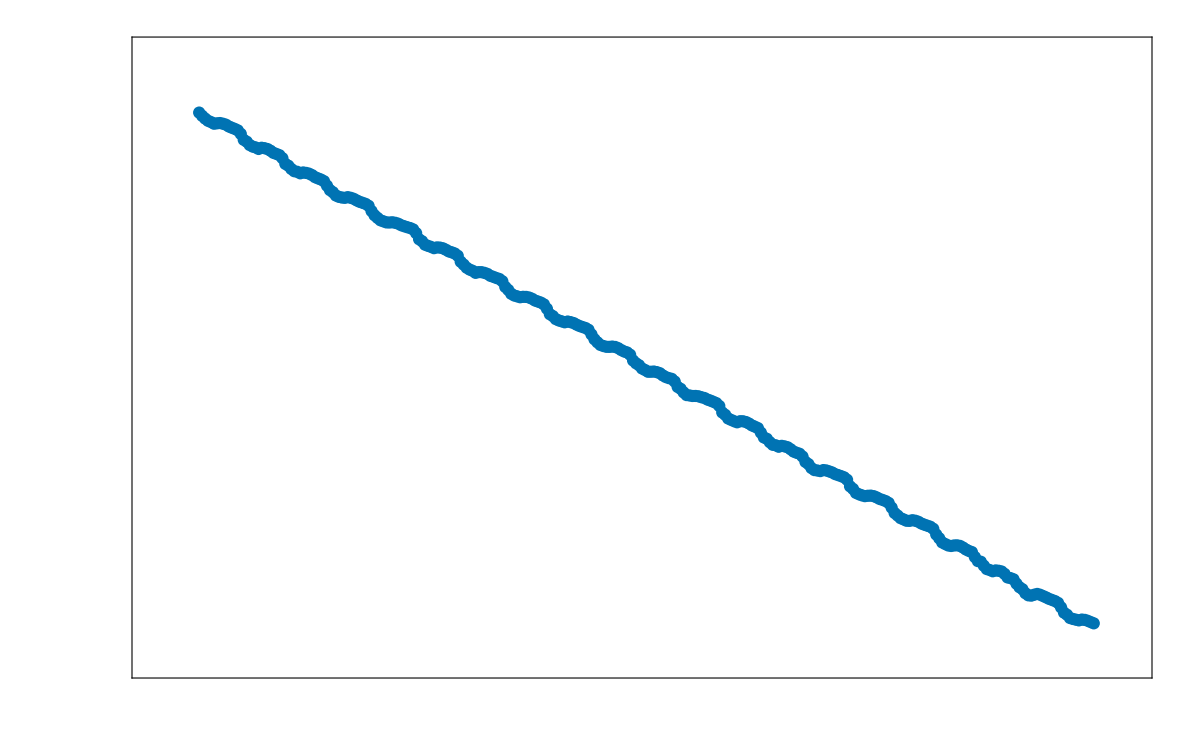

```mathematica
spinTrace =ListPlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_5cm_4hz.csv"], PlotRange->{{-0.5, 10.5}, {-70, 8}}, PlotStyle->{AbsoluteThickness[5], RGBColor[0.0,0.45,0.7]},
Axes->False,
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.025, 0}},{x,0,12,2}],Table[{y,, {0.015, 0}},{y,-70,1,10}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1200
]
```

```mathematica
Export["spinTrace.svg", spinTrace]
```

spinTrace.svg

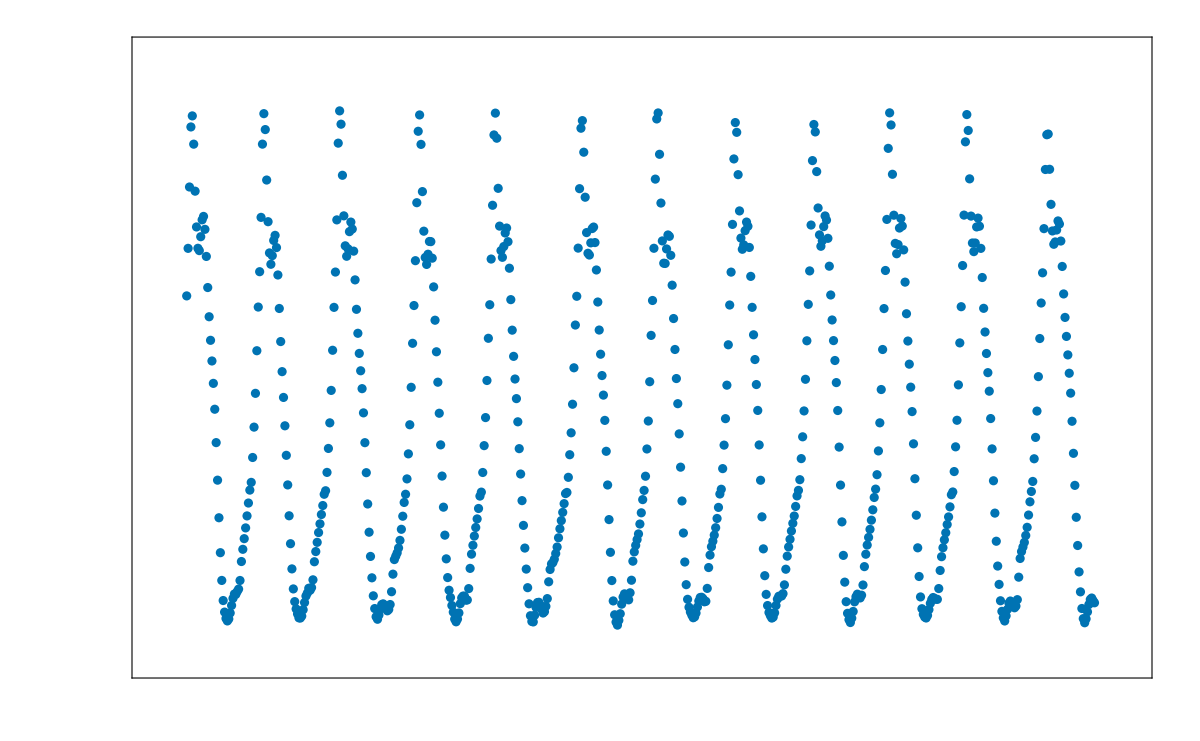

```mathematica
OscTrace =ListPlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_0deg\\Angles0deg_7cm_1hz.csv"], PlotRange->{{-0.8, 22.5}, {-0.45, 0.3}}, PlotStyle->{AbsoluteThickness[5], RGBColor[0.0,0.45,0.7]},
Frame->True,
Axes->False,
FrameStyle->Directive[Black, AbsoluteThickness[5]],
FrameTicks->{Table[{x, ,{0.025, 0}},{x,0,22,2}],Table[{y,, {0.015, 0}},{y,-0.5,0.3,0.1}]},FrameTicksStyle->Directive[Black, Bold,17],
ImageSize->1200
]
```

```mathematica
Export["OscTrace.svg", OscTrace]
```

OscTrace.svg